```mathematica
ejer=Graphics[{Gray,Line[{{-10,0},{10,0}}]}];
```

```mathematica
ejei=Graphics[{Gray,Line[{{0,-2},{0,10}}]}];
```

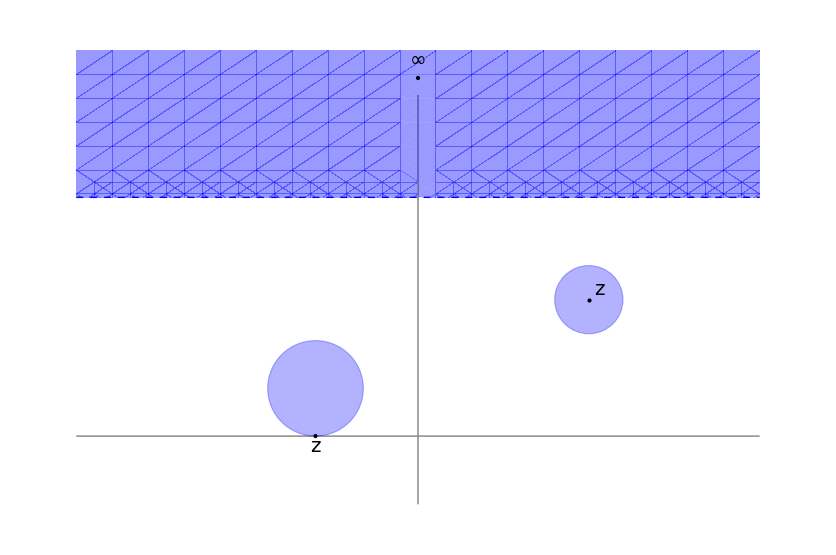

```mathematica
Show[ejer,ejei,
RegionPlot[y>7,{x,-10,10},{y,-2,11.3},BoundaryStyle->None,PlotStyle->{Directive[Blue,Opacity[0.4]]}],
Graphics[{Blue,Dashed,Thick,Line[{{-10,7},{10,7}}]}],
Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Blue,Opacity[0.3],Disk[{5,4},1]}],
Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Blue,Opacity[0.3],Disk[{-3,1.4},1.4]}],
Graphics[{Inset[Style["z",Italic,20],{5.3,4.3}],PointSize[Large],Point[{5,4}]}],
Graphics[{Inset[Style["∞",Italic,20],{0,11}],PointSize[Large],Point[{0,10.5}]}],
Graphics[{Inset[Style["z",Italic,20],{-3,-0.3}],PointSize[Large],Point[{-3,0}]}]
]
```

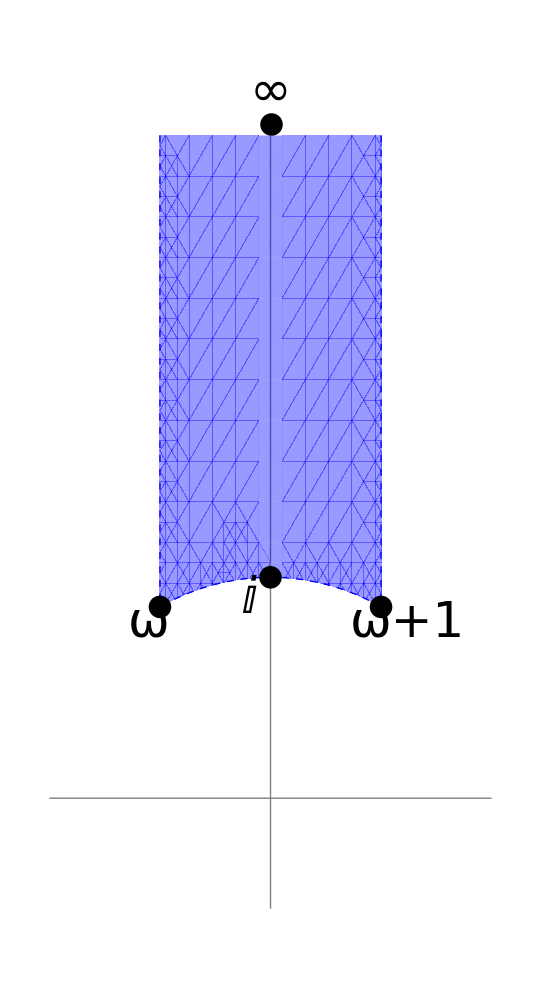

```mathematica
Show[Graphics[{Gray,Line[{{-1,0},{1,0}}]}],Graphics[{Gray,Line[{{0,-0.5},{0,3}}]}],
RegionPlot[x^2+y^2≥1&&Abs[x]≤0.5,{x,-1,1},{y,-0.5,3},BoundaryStyle->None,PlotStyle->{Directive[Blue,Opacity[0.4]]}],
Graphics[{Blue,Dashed,Thick,Line[{{-0.5,3},{-0.5,Sin[2π/3]}}]}],
Graphics[{Blue,Dashed,Thick,Line[{{0.5,3},{0.5,Sin[2π/3]}}]}],
ParametricPlot[{Cos[t],Sin[t]},{t,π-2π/3,2π/3},PlotStyle->{Dashed,Blue,Thick}],
Graphics[{Inset[Style["ⅈ",Italic,50],{-0.1,0.9}],PointSize[0.03],Point[{0,1}]}],
Graphics[{Inset[Style["ω",Italic,50],{Cos[2π/3]-0.05,Sin[2π/3]-0.07}],PointSize[0.03],Point[{Cos[2π/3],Sin[2π/3]}]}],
Graphics[{Inset[Style["ω+1",Italic,50],{Cos[2π/3]+1.12,Sin[2π/3]-0.07}],PointSize[0.03],Point[{Cos[2π/3]+1,Sin[2π/3]}]}],
Graphics[{Inset[Style["∞",Italic,50],{0,3.2}],PointSize[0.03],Point[{0,3.05}]}]
]
```